```mathematica
Subscript[g, n]=0.404;
B0= 2.35;
h = 6.626070040*10^(−34);
ℏ = h / (2*π);
Subscript[q, p]=1.6021766208*10^(−19);
Subscript[q, n]= 7 * Subscript[q, p];
Subscript[m, p]=1.6726219*10^(-27);
Subscript[m, n]=14*Subscript[m, p]; 
E2[B_]:= (ℏ*Subscript[g, n]*Subscript[q, n]*B^2)/(4*Subscript[m, n]*B0);
Subscript[ω, 0]=(Subscript[g, n]*Subscript[q, n]*B0)/(2*Subscript[m, n]);
E0[B_]:=Subscript[ω, 0]*ℏ;
```

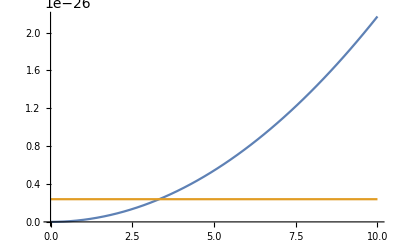

```mathematica
Plot[{E2[B], E0[B]}, {B, 0, 10}]
```

This calculation shows the sensitivity of the perturbation method as we see once we reach a neighborhood of field strengths near B0, the energy of the correction crosses the zeroth order energy. Below is the plot including the energy of each state to second order:

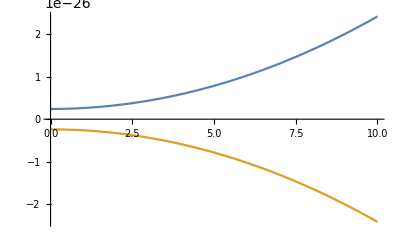

```mathematica
Plot[{E2[B]+E0[B],-E2[B]-E0[B]}, {B,0,10}]
```